# Single Susceptible Model

```mathematica
Clear["Global`*"]
```

```mathematica
pars={rA->10^-3,rB->0.25 10^-5,σ->10^-4,γ->3 10^-4,m->1,d->5 10^-4,β0->0.4,tMax->20000};
```

```mathematica
Κ=(rA-σ)/rB;
```

```mathematica
G1[t_] :=rA (s[0,t]+i[1,t])-rB (s[0,t]+i[1,t])^2  -β0/Κ b[t] s[0,t]-σ s[0,t]+γ i[1,t]
G2[t_] :=  β0/Κ  b[t] s[0,t]-σ i[1,t]-d i[1,t] -γ i[1,t]
G3[t_] := η i[1,t] - m b[t] -  β0/Κ  b[t]s[0,t]
```

## Equilibrium

```mathematica
equList={G1[t],G2[t],G3[t]};
vars={s[0,t],i[1,t],b[t]};
```

```mathematica
equi=Solve[equList=={0,0,0},vars]//Simplify
```

{{s[0,t]→0,i[1,t]→0,b[t]→0},{s[0,t]→(rA-σ)/rB,i[1,t]→0,b[t]→0},{s[0,t]→-(m (rA-σ) (d+γ+σ))/(rB β0 (d+γ-η+σ)),i[1,t]→1/(2 rB^2 β0^2 (d+γ-η+σ)^2)(-d^3 rB β0^2+2 m rA rB β0 γ^2+rA rB β0^2 γ^2-2 m rA rB β0 γ η-2 rA rB β0^2 γ η+rA rB β0^2 η^2+d^2 rB β0 (β0 (rA-2 γ+2 η-3 σ)+2 m (rA-σ))+4 m rA rB β0 γ σ+2 rA rB β0^2 γ σ-2 m rB β0 γ^2 σ-rB β0^2 γ^2 σ-2 m rA rB β0 η σ-2 rA rB β0^2 η σ+2 m rB β0 γ η σ+2 rB β0^2 γ η σ-rB β0^2 η^2 σ+2 m rA rB β0 σ^2+rA rB β0^2 σ^2-4 m rB β0 γ σ^2-2 rB β0^2 γ σ^2+2 m rB β0 η σ^2+2 rB β0^2 η σ^2-2 m rB β0 σ^3-rB β0^2 σ^3+d rB β0 (β0 (2 rA-γ+η-3 σ) (γ-η+σ)+2 m (rA-σ) (2 γ-η+2 σ))-√(rB^2 β0^3 (d+γ-η+σ)^3 (d^3 β0+β0 (rA-σ)^2 (γ-η+σ)+d (rA-σ) (rA β0+β0 (-2 γ+2 η-3 σ)-4 m (γ+σ))+d^2 (-4 m (rA-σ)+β0 (-2 rA+γ-η+3 σ))))),b[t]→1/(2 m rB^2 β0^2 (d+γ-η+σ))(d^3 rB β0^2-2 m rA rB β0 γ^2-rA rB β0^2 γ^2+2 m rA rB β0 γ η+2 rA rB β0^2 γ η-rA rB β0^2 η^2+d^2 rB β0 (-β0 (rA-2 γ+2 η-3 σ)-2 m (rA-σ))-4 m rA rB β0 γ σ-2 rA rB β0^2 γ σ+2 m rB β0 γ^2 σ+rB β0^2 γ^2 σ+2 m rA rB β0 η σ+2 rA rB β0^2 η σ-2 m rB β0 γ η σ-2 rB β0^2 γ η σ+rB β0^2 η^2 σ-2 m rA rB β0 σ^2-rA rB β0^2 σ^2+4 m rB β0 γ σ^2+2 rB β0^2 γ σ^2-2 m rB β0 η σ^2-2 rB β0^2 η σ^2+2 m rB β0 σ^3+rB β0^2 σ^3+d rB β0 (-β0 (2 rA-γ+η-3 σ) (γ-η+σ)-2 m (rA-σ) (2 γ-η+2 σ))+√(rB^2 β0^3 (d+γ-η+σ)^3 (d^3 β0+β0 (rA-σ)^2 (γ-η+σ)+d (rA-σ) (rA β0+β0 (-2 γ+2 η-3 σ)-4 m (γ+σ))+d^2 (-4 m (rA-σ)+β0 (-2 rA+γ-η+3 σ)))))},{s[0,t]→-(m (rA-σ) (d+γ+σ))/(rB β0 (d+γ-η+σ)),i[1,t]→1/(2 rB^2 β0^2 (d+γ-η+σ)^2)(-d^3 rB β0^2+2 m rA rB β0 γ^2+rA rB β0^2 γ^2-2 m rA rB β0 γ η-2 rA rB β0^2 γ η+rA rB β0^2 η^2+d^2 rB β0 (β0 (rA-2 γ+2 η-3 σ)+2 m (rA-σ))+4 m rA rB β0 γ σ+2 rA rB β0^2 γ σ-2 m rB β0 γ^2 σ-rB β0^2 γ^2 σ-2 m rA rB β0 η σ-2 rA rB β0^2 η σ+2 m rB β0 γ η σ+2 rB β0^2 γ η σ-rB β0^2 η^2 σ+2 m rA rB β0 σ^2+rA rB β0^2 σ^2-4 m rB β0 γ σ^2-2 rB β0^2 γ σ^2+2 m rB β0 η σ^2+2 rB β0^2 η σ^2-2 m rB β0 σ^3-rB β0^2 σ^3+d rB β0 (β0 (2 rA-γ+η-3 σ) (γ-η+σ)+2 m (rA-σ) (2 γ-η+2 σ))+√(rB^2 β0^3 (d+γ-η+σ)^3 (d^3 β0+β0 (rA-σ)^2 (γ-η+σ)+d (rA-σ) (rA β0+β0 (-2 γ+2 η-3 σ)-4 m (γ+σ))+d^2 (-4 m (rA-σ)+β0 (-2 rA+γ-η+3 σ))))),b[t]→1/(2 m rB^2 β0^2 (d+γ-η+σ))(d^3 rB β0^2-2 m rA rB β0 γ^2-rA rB β0^2 γ^2+2 m rA rB β0 γ η+2 rA rB β0^2 γ η-rA rB β0^2 η^2+d^2 rB β0 (-β0 (rA-2 γ+2 η-3 σ)-2 m (rA-σ))-4 m rA rB β0 γ σ-2 rA rB β0^2 γ σ+2 m rB β0 γ^2 σ+rB β0^2 γ^2 σ+2 m rA rB β0 η σ+2 rA rB β0^2 η σ-2 m rB β0 γ η σ-2 rB β0^2 γ η σ+rB β0^2 η^2 σ-2 m rA rB β0 σ^2-rA rB β0^2 σ^2+4 m rB β0 γ σ^2+2 rB β0^2 γ σ^2-2 m rB β0 η σ^2-2 rB β0^2 η σ^2+2 m rB β0 σ^3+rB β0^2 σ^3+d rB β0 (-β0 (2 rA-γ+η-3 σ) (γ-η+σ)-2 m (rA-σ) (2 γ-η+2 σ))-√(rB^2 β0^3 (d+γ-η+σ)^3 (d^3 β0+β0 (rA-σ)^2 (γ-η+σ)+d (rA-σ) (rA β0+β0 (-2 γ+2 η-3 σ)-4 m (γ+σ))+d^2 (-4 m (rA-σ)+β0 (-2 rA+γ-η+3 σ)))))}}

### Check the equilibria validation

```mathematica
Reduce[{0<(s[0,t]/.equi[[3]]),0<(i[1,t]/.equi[[3]]),0<(b[t]/.equi[[3]]),0<m,0<rA,0<σ,0<d,0<γ,0<η,0<β0,0<rB,σ<rA},η]
```

False

```mathematica
Reduce[{0<(s[0,t]/.equi[[4]]),0<(i[1,t]/.equi[[4]]),0<(b[t]/.equi[[4]]),0<m,0<rA,0<σ,0<d,0<γ,0<η,0<β0,0<rB,σ<rA},η]//Simplify
```

σ>0&&rA>σ&&d>0&&β0>0&&m>0&&γ>0&&rB>0&&η>((m+β0) (d+γ+σ))/β0

This gives us an critical threshold for the beetle emergence rate parameter “η “  which can be thought as an expression for the basic reproductive number

```mathematica
ηCrit = ((d+γ+σ) (m+β0))/β0;
```

```mathematica
ηCrit /.pars
```

0.00315

## Numerical Equilibrium

```mathematica
parsη[ηIn_]:={rA->10^-3,rB->0.25 10^-5,σ->10^-4,γ->3 10^-4,m->1,d->5 10^-4,β0->0.4,tMax->20000,η->ηIn};
```

```mathematica
Leg=LineLegend[{Gray,Black,Directive[Gray,Dashed]},{"Stable Beetle-Free","Stable Endemic","Unstable Beetle-Free"}];
```

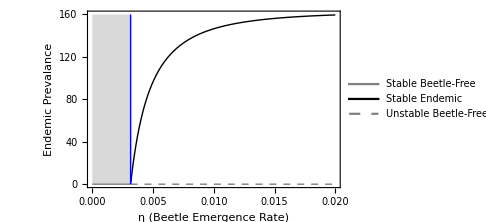

```mathematica
Show[
(*Endemic*)
Plot[(i[1,t]/.equi[[4]]/.parsη[η]),{η,ηCrit/.parsη[η],0.02},PlotStyle->Directive[Black,Thick],PlotRange->All],
(*Disease Free*)
Plot[0,{η,0,ηCrit/.parsη[η]},PlotStyle->Directive[Gray,Thick],Filling->160,FillingStyle->LightGray],
Plot[0,{η,ηCrit/.parsη[η],0.02},PlotStyle->Directive[Gray,Dashed,Thick]],
(*ηCrit*)
ListLinePlot[{{ηCrit/.parsη[η],0},{ηCrit/.parsη[η],160}},PlotStyle->Directive[Blue,Thick]],
(*Plotting Options*)
PlotRange->{{0,All},{0,160}},Axes->False,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[{Black,12}],FrameStyle->Directive[{Thickness[0.002],Black}],Epilog->{{Inset[Leg,Scaled[{0.6,0.6}]]} },FrameTicks->{{True,False},{True,False}},FrameLabel->{"η (Beetle Emergence Rate)","Endemic Prevalance"}
]
```

```mathematica
Points={{0.0025,40},{0.005,40},{0.0075,40},{0.01,40}};
Labels={"i","ii","iii","iv"};
```

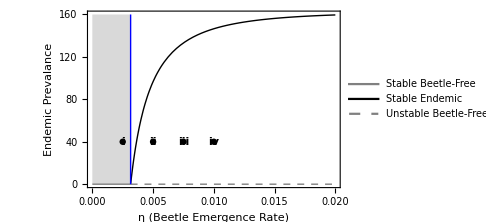

```mathematica
Show[
(*Endemic*)
Plot[(i[1,t]/.equi[[4]]/.parsη[η]),{η,ηCrit/.parsη[η],0.02},PlotStyle->Directive[Black,Thick],PlotRange->All],
(*Disease Free*)
Plot[0,{η,0,ηCrit/.parsη[η]},PlotStyle->Directive[Gray,Thick],Filling->160,FillingStyle->LightGray],
Plot[0,{η,ηCrit/.parsη[η],0.02},PlotStyle->Directive[Gray,Dashed,Thick]],
(*ηCrit*)
ListLinePlot[{{ηCrit/.parsη[η],0},{ηCrit/.parsη[η],160}},PlotStyle->Directive[Blue,Thick]],
(*Points*)
ListPlot[Points,AxesOrigin->{0,0},PlotStyle->Black],
(*Plotting Options*)
PlotRange->{{0,All},{0,160}},Axes->False,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[{Black,12}],FrameStyle->Directive[{Thickness[0.002],Black}],Epilog->{{Inset[Leg,Scaled[{0.6,0.6}]]},{Table[Text[Style[Labels[[i]],Black,Bold],Points[[i]],{2,-0.6}],{i,Length[Points]}]} },FrameTicks->{{True,False},{True,False}},FrameLabel->{"η (Beetle Emergence Rate)","Endemic Prevalance"}
]
```

## Numerical Dynamics

Numerical dynamics for parameter choices i-iv

```mathematica
odes= {D[s[0,t],t]==G1[t],D[i[1,t],t]==G2[t],D[b[t],t]==G3[t]};
init = {s[0,0]== Κ,i[1,0]==i0,b[0]==10}/.pars;
```

```mathematica
NSol[i0In_,ηIn_]:=NDSolve[{odes,init/.i0->i0In}/.parsη[ηIn],vars, {t,0,tMax/.parsη[ηIn]}]//Flatten;
```

```mathematica
NumDynPlot[i0In_,ηIn_,lab_]:=Block[{NumSol},
NumSol=NSol[i0In,ηIn];
Show[
(*endemic*)
Plot[Evaluate[i[1,t]/.NumSol],{t,0,tMax/.parsη[ηIn]},PlotStyle->{Red},Frame->True,PlotRange->{{0,tMax/.parsη[ηIn]},{0,250}},FrameStyle->Directive[{Thickness[0.002],Black}],FrameTicksStyle->Directive[{Black,12}],LabelStyle->Black,Epilog->{Text[Style[lab,12],Scaled[{0.97,0.94}]]},ImageSize->Large,Axes->None,FrameTicks->{{True,False},{True,False}},Filling->Axis,FillingStyle->LightPink],
(*equilibrium*)
ListLinePlot[{{0,i[1,t]/.equi[[4]]/.parsη[ηIn]},{tMax/.parsη[ηIn],i[1,t]/.equi[[4]]/.parsη[ηIn]}},PlotStyle->Directive[Gray],PlotRange->All]
]]
```

```mathematica
Dplt1= NumDynPlot[40,0.0025,"i"];
Dplt2= NumDynPlot[40,0.005,"ii"];
Dplt3= NumDynPlot[40,0.0075,"iii"];
Dplt4=NumDynPlot[40,0.01,"iv"];
```

```mathematica
LegNumDyn=LineLegend[{Red,Directive[Gray]},{"Numerical Integration","Endemic Equilibrium"}];
```

```mathematica
ResourceFunction["PlotGrid"][{{Dplt1,Dplt2},{Dplt3,Dplt4}},ImageSize->Large,PlotRange->Max,Epilog->{{Inset[LegNumDyn,Scaled[{0.2,0.85}]]}},FrameLabel->{"Time per 1000 days","Incidence"}]
```

-Graphics-

## Stochastic Simulations (Gillespie Algorithm)

```mathematica
Clear[rates,ΔState,testPars]
```

```mathematica
Rates[S_]:={Max[rA (S[[2]]+S[[3]])-rB (S[[2]]+S[[3]])^2,0],σ S[[2]],β0/Κ S[[4]] S[[2]],d S[[3]]+σ S[[3]],η S[[3]],m S[[4]],γ S[[3]]};
ΔState[Δt_]:={{Δt,1,0,0},{Δt,-1,0,0},{Δt,-1,1,-1},{Δt,0,-1,0},{Δt,0,0,1},{Δt,0,0,-1},{Δt,1,-1,0}};
```

```mathematica
Pars[tMaxIn_]:={rA->10^-3,rB->0.25 10^-5,σ->10^-4,γ->3 10^-4,m->1,d->5 10^-4,β0->0.4,tMax->tMaxIn};
```

```mathematica
Clear[sim]
sim[i0In_,ηIn_,intS_]:=sim[i0In,ηIn,intS]=Block[{out,temp,Δt,e},
out={{0,S0,I0,B0}}/.{S0->Κ/.parsη[ηIn],B0-> 10 }/.{I0->i0In}/.parsη[ηIn];
temp=Rates[out[[-1]]]/.{I0->i0In}/.parsη[ηIn]//Chop;
Δt=RandomVariate[ExponentialDistribution[Total[temp]]];
While[out[[-1,1]]+Δt<=tMax/.{I0->i0In}/.parsη[ηIn],
e=RandomChoice[temp->{1,2,3,4,5,6,7}];
AppendTo[out,out[[-1]]+ΔState[Δt][[e]]];
temp=Rates[out[[-1]]]/.{I0->i0In}/.parsη[ηIn]//Chop;
If[Total[temp]>0  ,Δt=RandomVariate[ExponentialDistribution[Total[temp]]],Δt=tMax/.parsη[ηIn]];
 ];
  AppendTo[out,Join[{tMax/.parsη[ηIn]},out[[-1,2;;]]]]
]
```

```mathematica
Clear[SInt,IInt,BInt]
SInt[i0In_,ηIn_,intS_]:=SInt[i0In,ηIn,intS]=Interpolation[sim[i0In,ηIn,intS][[;;,{1,2}]],InterpolationOrder->0]
IInt[i0In_,ηIn_,intS_]:=IInt[i0In,ηIn,intS]=Interpolation[sim[i0In,ηIn,intS][[;;,{1,3}]],InterpolationOrder->0]
BInt[i0In_,ηIn_,intS_]:=BInt[i0In,ηIn,intS]=Interpolation[sim[i0In,ηIn,intS][[;;,{1,4}]],InterpolationOrder->0]
```

#### Mean

```mathematica
MeanSTab[i0In_,ηIn_]:=Table[{t,Mean[Table[SInt[i0In,ηIn,intS][t],{intS,1,50}]]},{t,0,tMax/.parsη[ηIn],tMax/100./.parsη[ηIn]}]
MeanITab[i0In_,ηIn_]:=Table[{t,Mean[Table[IInt[i0In,ηIn,intS][t],{intS,1,50}]]},{t,0,tMax/.parsη[ηIn],tMax/100./.parsη[ηIn]}]
```

#### Confidence Interval

```mathematica
CISTab[i0In_,ηIn_]:={Table[{t,Mean[Table[SInt[i0In,ηIn,intS][t],{intS,1,50}]]+2StandardDeviation[Table[SInt[i0In,ηIn,intS][t],{intS,1,50}]]},{t,0,tMax/.parsη[ηIn],tMax/100./.parsη[ηIn]}],
Table[{t,Mean[Table[SInt[i0In,ηIn,intS][t],{intS,1,50}]]-2StandardDeviation[Table[SInt[i0In,ηIn,intS][t],{intS,1,50}]]},{t,0,tMax/.parsη[ηIn],tMax/100./.parsη[ηIn]}]}
CIITab[i0In_,ηIn_]:={Table[{t,Mean[Table[IInt[i0In,ηIn,intS][t],{intS,1,50}]]+2StandardDeviation[Table[IInt[i0In,ηIn,intS][t],{intS,1,50}]]},{t,0,tMax/.parsη[ηIn],tMax/100./.parsη[ηIn]}],
Table[{t,Mean[Table[IInt[i0In,ηIn,intS][t],{intS,1,50}]]-2StandardDeviation[Table[IInt[i0In,ηIn,intS][t],{intS,1,50}]]},{t,0,tMax/.parsη[ηIn],tMax/100./.parsη[ηIn]}]}
```

#### Visualization

```mathematica
parsη[ηIn_]:={rA->10^-3,rB->0.25 10^-5,σ->10^-4,γ->3 10^-4,m->1,d->5 10^-4,β0->0.4,tMax->20000,η->ηIn};
```

```mathematica
simPlot[i0In_,ηIn_,lab_]:=Show[
(*Susceptible*)
Plot[Table[SInt[i0In,ηIn,intS][t],{intS,1,50}],{t,0,tMax/.parsη[ηIn]},PlotStyle->Directive[Blue,Opacity[0.05]]],
ListLinePlot[MeanSTab[i0In,ηIn],PlotStyle->Directive[Blue,Thick]],
ListLinePlot[CISTab[i0In,ηIn],PlotStyle->Directive[Lighter[Orange],Thick]],
(*Infected*)
Plot[Table[IInt[i0In,ηIn,intS][t],{intS,1,50}],{t,0,tMax/.parsη[ηIn]},PlotStyle->Directive[Red,Opacity[0.05]]],
ListLinePlot[MeanITab[i0In,ηIn],PlotStyle->Directive[Red,Thick]],
ListLinePlot[CIITab[i0In,ηIn],PlotStyle->Directive[Lighter[Orange],Thick]],
(*Plotting Options*)
Axes->None ,PlotRange->{All,All},Frame->True,ImageSize->Large,FrameStyle->Directive[{Thickness[0.002],Black}],
FrameTicksStyle->Directive[{Black,12}],LabelStyle->Black,Epilog->{{Text[Style[lab,12],Scaled[{0.94,0.94}]]}},FrameTicks->{{True,False},{True,False}}]
```

```mathematica
plt1=simPlot[40,0.0025,"i"];
plt2 = simPlot[40,0.005,"ii"];
plt3 = simPlot[40,0.0075,"iii"];
plt4 = simPlot[40,0.01,"iv"];
```

```mathematica
LegStoch=LineLegend[{Blue,Red},{"",""}];
```

```mathematica
ResourceFunction["PlotGrid"][{{plt1,plt2},{plt3,plt4}},FrameLabel->{Text[Style["Time (days)",12]],Text[Style["Population Dynamics",12]]},ImageSize->Large,PlotRange->Max,Epilog->{{Inset[LegStoch,Scaled[{0.85,0.4}]]}}]
```

-Graphics-

```mathematica
NumDynPlot2[i0In_,ηIn_,lab_]:=Block[{NumSol},
NumSol=NSol[i0In,ηIn];
Show[
(*endemic*)
Plot[Evaluate[i[1,t]/.NumSol],{t,0,tMax/.parsη[ηIn]},PlotStyle->{Red},Frame->True,PlotRange->{{0,tMax/.parsη[ηIn]},{0,250}},FrameStyle->Directive[{Thickness[0.002],Black}],FrameTicksStyle->Directive[{Black,12}],LabelStyle->Black,Epilog->{Text[Style[lab,12],Scaled[{0.97,0.94}]]},ImageSize->Large,Axes->None,FrameTicks->{{True,False},{True,False}},Filling->Axis,FillingStyle->LightPink],
(*Infested Stochastic Simulations Mean*)
ListLinePlot[MeanITab[i0In,ηIn],PlotStyle->Directive[Black,Dashed,Thick],PlotRange->All],
(*equilibrium*)
ListLinePlot[{{0,i[1,t]/.equi[[4]]/.parsη[ηIn]},{tMax/.parsη[ηIn],i[1,t]/.equi[[4]]/.parsη[ηIn]}},PlotStyle->Directive[Gray],PlotRange->All]
]]
```

```mathematica
p1=NumDynPlot2[40,0.0025,i];
p2 =NumDynPlot2[40,0.005,ii];
p3 =NumDynPlot2[40,0.0075,iii];
p4 =NumDynPlot2[40,0.01,iv];
```

```mathematica
leg3=LineLegend[{Red,Directive[Black,Dashed],Directive[Gray]},{"Numerical Integration","Stochastic Simulations Mean","Endemic Equilibrium"}];
```

```mathematica
ResourceFunction["PlotGrid"][{{p1,p2},{p3,p4}},FrameLabel->{"Time (1000 days)","Incidence"},ImageSize->Large,PlotRange->Max,Epilog->{{Inset[leg3,Scaled[{0.2,0.85}]]}}]
```

-Graphics-

## Cut at time t = 1000

```mathematica
data = Table[{1000,Table[IInt[40,0.005,intS][1000],{intS,1,50}][[i]]},{i,1,50}];
```

```mathematica
ResourceFunction["PlotGrid"][{{
Show[
(*Histogram*)
Histogram[Table[IInt[40,0.005,intS][1000],{intS,1,50}],10,"PDF",BarOrigin->Left,PlotRangePadding->0,PlotRange->{All,All}],
(*Normal Distribution*)
ParametricPlot[{PDF[NormalDistribution[Mean[Table[IInt[40,0.005,intS][1000],{intS,1,50}]],StandardDeviation[Table[IInt[40,0.005,intS][1000],{intS,1,50}]]],x],x},{x,150,240},PlotStyle->{Black,Thick},PlotRange->All],Frame->True,FrameTicks->{{True,False},{True,False}},PlotRangePadding->0,GridLines->{None,Automatic},FrameLabel->{"Frequency","Incidence"}],
(*Points*)
ListPlot[data,Sequence[Axes->False,Frame->True,GridLines->Automatic,PlotRangePadding->0,PlotRange->{{990,1010},{40,90}}],
FrameLabel->{"Time","Incidence"}]}},
(*Plotting Options*)
"MergeAxes"->None,ImageSize->Large]
```

-Graphics-

### Correlation

Considering case “ii”

```mathematica
dataIS =Table[{IInt[40,0.005,intS][1000],SInt[40,0.005,intS][1000]},{intS,1,500}];
dataIB =Table[{IInt[40,0.005,intS][1000],BInt[40,0.005,intS][1000]},{intS,1,500}];
dataSB = Table[{SInt[40,0.005,intS][1000],BInt[40,0.005,intS][1000]},{intS,1,500}];
```

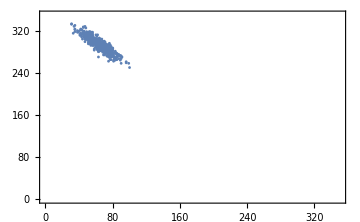
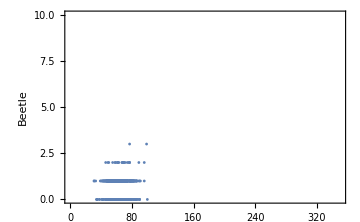
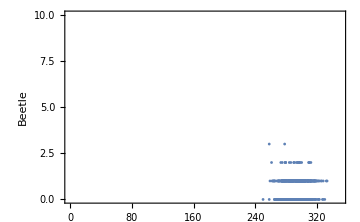

```mathematica
Row[{
(*I versus S*)
ListPlot[dataIS,Frame->True,FrameLabel->{"",""},ImageSize->Medium,FrameStyle->Directive[{Thickness[0.002],Black}],FrameTicksStyle->Directive[{Black,12}],LabelStyle->Black,PlotRange->{{0,350},{0,350}}],
(*I versus B*)
ListPlot[dataIB,Frame->True,FrameLabel->{"","Beetle"},ImageSize->Medium,FrameStyle->Directive[{Thickness[0.002],Black}],FrameTicksStyle->Directive[{Black,12}],LabelStyle->Black,PlotRange->{{0,350},{0,10}}],
(*S versus B*)
ListPlot[dataSB,Frame->True,FrameLabel->{"","Beetle"},ImageSize->Medium,FrameStyle->Directive[{Thickness[0.002],Black}],FrameTicksStyle->Directive[{Black,12}],LabelStyle->Blue,PlotRange->{{0,350},{0,10}}]}]
```

Based on the figures  and  are strongly correlated! Therefore, we just focus on the  versus

### Fitting Line

```mathematica
First[RegionConvert[RegionFit[dataIS,"Line"],"Implicit"]]
```

1. x+1. y==359.

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

```mathematica
Line1=MaTeX[" I_1 = -1.2069 S_0 + 526.931",Magnification->1.2];
```

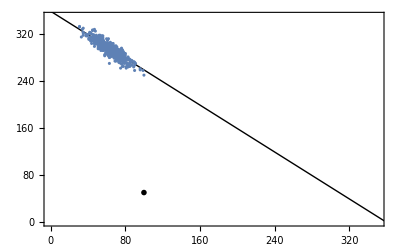

```mathematica
Show[ListPlot[dataIS,Frame->True,FrameLabel->{"",""},ImageSize->400,FrameStyle->Directive[{Thickness[0.002],Black}],FrameTicksStyle->Directive[{Black,12}],LabelStyle->Black,PlotRange->{{0,350},{0,350}},Epilog->Inset[Line1,{100,50}]],Graphics[RegionFit[dataIS,"Line"]]]
```

### Using Correlation Definition

correlation coefficient that measures linear correlation between two sets of data. 
It is the ratio between the covariance of two variables and the product of their standard deviations; thus, it is essentially a normalized measurement of the covariance

```mathematica
ITab=dataIS[[;;,1]];
STab = dataIS[[;;,2]];
```

```mathematica
rho[x_,y_] := Covariance[x,y]/(Sqrt[Variance[x]]Sqrt[Variance[y]])
```

```mathematica
rho[ITab,STab]
```

-0.893646